```mathematica
Integrate[Exp[-Cos[2 ϕ]],{ϕ,0,π}]
```

π BesselI[0,1]

```mathematica
N[π BesselI[0,1]]
```

3.97746

```mathematica
FindMaximum[{Exp[-Cos[2 ϕ]],0< ϕ < π},{ϕ, 1.5}]
```

{2.71828,{ϕ→1.5708}}

```mathematica
Integrate[1/(3.97746) Exp[-Cos[2 ϕ]],{ϕ,0,ϕ0}]
```

∫_0^ϕ0 0.251417 ⅇ^(-Cos[2 ϕ])ⅆϕ

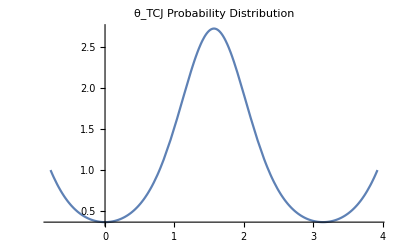

```mathematica
Plot[{Exp[-Cos[2ϕ]] },{ϕ,-π/4,5π/4}, PlotLabel-> "θ_TCJ Probability Distribution"]
```

```mathematica
datapts = Table[{ϕ,1/(3.977463260506422)(Exp[-Cos[2ϕ]])},{ϕ, 0, 3.141, 3.141/100}];
```

Generating 100 data points for Gaussian fit.

```mathematica
NonlinearModelFit[datapts, A*Exp[-(ϕ-π/2)^2/(2σ2)] + P0, {A, μ,σ2, P0}, ϕ]
```

FittedModel[1.74843×10^7-1.74843×10^7 ⅇ^(«23» («1»)^2)]

```mathematica
Normal[%]
```

1.74843×10^7-1.74843×10^7 ⅇ^(1.38748×10^-8 (-π/2+ϕ)^2)

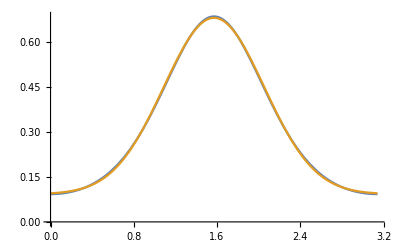

```mathematica
Plot[{1/(3.977463260506422) Exp[-Cos[2ϕ]] ,0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)},{ϕ,0,π}]
```

```mathematica
N[π/2]
```

1.5708

```mathematica
σsq = 1/(2*2.136298328298766)
```

0.23405

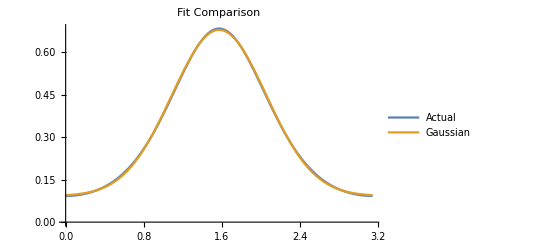

```mathematica
Plot[{1/(3.977463260506422) Exp[-Cos[2ϕ]] ,0.092107+0.586627 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)},{ϕ,0,π}, PlotLegends-> LineLegend[{"Actual","Gaussian"}], PlotLabel->"Fit Comparison"]
```

```mathematica
Res[ϕ_]:= 1/(3.977463260506422) Exp[-Cos[2ϕ]]  - (0.092107+0.586627 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2))
```

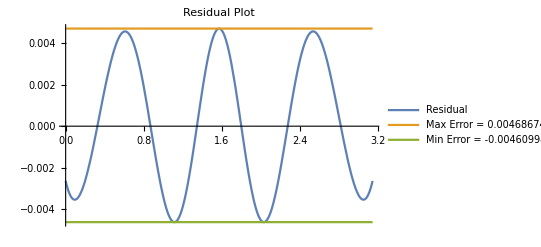

```mathematica
Plot[{Res[ϕ], 0.00469, -0.00461},{ϕ,0,π}, PlotLabel-> "Residual Plot", PlotLegends-> LineLegend[{"Residual","Max Error = 0.00468674", "Min Error = -0.00460998"} ]]
```

```mathematica
FindMaximum[{Res[ϕ], 0≤ ϕ ≤ π/2},{ϕ, 1.5}]
```

{0.00468674,{ϕ→1.56935}}

```mathematica
FindMinimum[{Res[ϕ], 0≤ ϕ ≤ π/2},{ϕ, 1.0}]
```

{-0.00460998,{ϕ→1.11303}}

Fit parameters for Gaussian: A Exp[-( x - π/2 ) / (2 σ2)] + P_0

I fitted for 3 parameters because I know that the maximum of the initial probability distribution was π/2. I also fitted for σ^2 instead of σ, just in case it made the solver’s job easier.

P_0 = 0.092107
A = 0.586627
σ^2= 0.23405

I also truncated to 6 sig figs since it did not affect the fit that much.

Untruncated Residual:

```mathematica
Res2[ϕ_] :=1/(3.977463260506422) Exp[-Cos[2ϕ]] -  0.09210758442693216-0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)
```

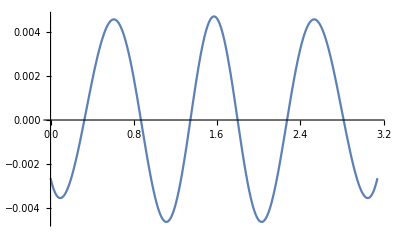

```mathematica
Plot[Res2[ϕ], {ϕ,0,π}]
```

So then, approximate P(θ-θ_TCJ):

```mathematica
P[ϕ_]:= 0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2)
```

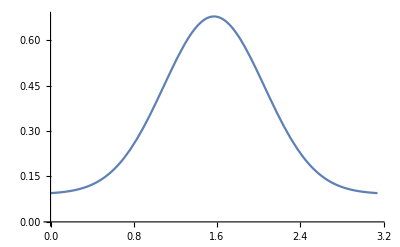

```mathematica
Plot[P[ϕ],{ϕ,0,π}]
```

```mathematica
NF =Integrate[P[ϕ],{ϕ,0,π}]
```

0.999922

New factor by which we should normalize this new distribution

```mathematica
Pn[ϕ_]:= 1/(0.999922)*(0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2))
```

```mathematica
NF2 = Integrate[Pn[ϕ],{ϕ,0,π}]
```

1.

```mathematica
Res3[ϕ_] :=1/(3.977463260506422) Exp[-Cos[2ϕ]] -  (0.09210758442693216+0.5866273359249808 ⅇ^(-2.136298328298766 (-1.5707963663387658+ϕ)^2))*(1/0.999922)
```

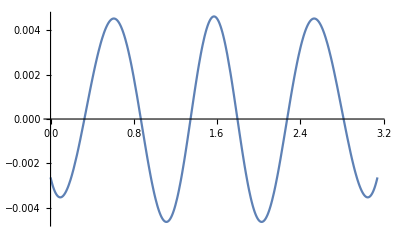

```mathematica
Plot[Res3[ϕ], {ϕ,0,π}]
```

Now in theory, if I can manipulate C++‘s normal distribution to make this distribution work, we should be good to go. The standard normal distribution does not have a constant offset however. So I should see if I can use some stats tricks to artificially construct my offset normal distribution.

```mathematica
F[ϕ0_]:= Integrate[Pn[ϕ],{ϕ,0,ϕ0}]
```

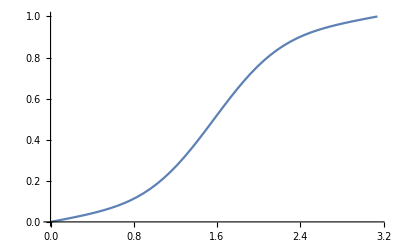

Integrate::ilim: Invalid integration variable or limit(s) in {0.0000641782,0,π}.

NIntegrate::itraw: Raw object 0.0000641782 cannot be used as an iterator.

Integrate::ilim: Invalid integration variable or limit(s) in {0.0641783,0,π}.

NIntegrate::itraw: Raw object 0.0641783 cannot be used as an iterator.

General::stop: Further output of NIntegrate::itraw will be suppressed during this calculation.

Integrate::ilim: Invalid integration variable or limit(s) in {0.128292,0,π}.

General::stop: Further output of Integrate::ilim will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[F[ϕ0],{ϕ0,0,π}]
```